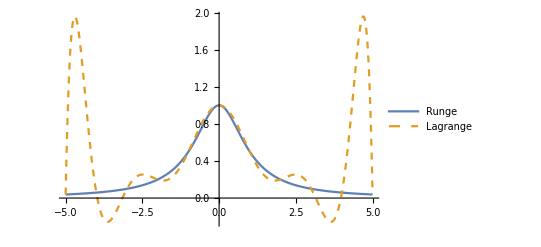

```mathematica
(** a **)
Remove["Global`*"]

R[x_]:= 1/(x^2+1)

y =Table[-5+k,{k,0,10}];

r =Table[R[y[[k]]],{k,1,11}];

L[x_] := Table[Product[If[i≠k,(x-y[[i]])/(y[[k]]-y[[i]]),1],{i,1,11}],{k,1,11}]

P[x_]:=Sum[R[y[[k]]]L[x][[k]],{k,1,11}]

Plot[{R[x],P[x]},{x,-5,5},PlotStyle->{Thick,Dashed}, PlotLegends->{"Runge","Lagrange"}]
```

```mathematica
(** What we observe from the above plot is that the Lagrange interpolating polynomial does a good job of representing the function on [-2,2] but a poor job of representing the function outside that region. **)
```

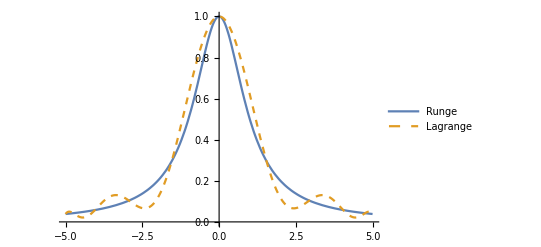

```mathematica
(** c **)
Remove["Global`*"]

R[x_]:= 1/(x^2+1)

y =Table[5Cos[(k Pi)/10],{k,0,10}]//N ;

r =Table[R[y[[k]]],{k,1,11}];

L[x_] := Table[Product[If[i≠k,(x-y[[i]])/(y[[k]]-y[[i]]),1],{i,1,11}],{k,1,11}]

P[x_]:=Sum[R[y[[k]]]L[x][[k]],{k,1,11}]

Plot[{R[x],P[x]},{x,-5,5},PlotStyle->{Thick,Dashed}, PlotLegends->{"Runge","Lagrange"}]
```

```mathematica
(** This time, the Lagrange polynomial does a better job of approximating the Runge function over the entire interval. **)
```